## Recursion equation for Random Walk hitting time (Section 4.3)

Consider the first hitting time for the Random Walk on {0,1,...,M} to the target winning level {M}. We can solve for it using Theorem 4.4. What is the behavior when M grows?

### Assume first that q is not 1/2. The Recursion Equation is homogeneous, and its solution has the form:

```mathematica
RSolveValue[{q*h[x+1]-h[x]+(1-q)*h[x-1]==0,h[0]==0,h[M]==1},h[x],x]
```

(-1+((1-q)/q)^x)/(-1+((1-q)/q)^M)

### Let' s plot with the value x = 1:

```mathematica
F[M_,q_]:=((-1+((1-q)/q)^x)/(-1+((1-q)/q)^M))/.{x->1};
```

Plotting for some q’s less than 1/2:

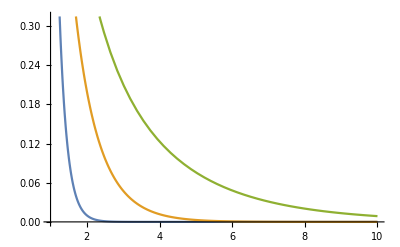

```mathematica
Plot[{F[M,.01],F[M,.2],F[M,.4]},{M,1,10}]
```

Plotting for some q' s greater than 1/2:

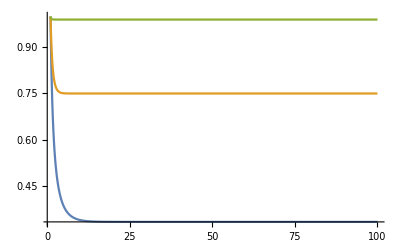

```mathematica
Plot[{F[M,.6],F[M,.8],F[M,.99]},{M,1,100}]
```

Example limits:

```mathematica
Limit[F[M,.1],M->Infinity]
Limit[F[M,.45],M->Infinity]
Limit[F[M,.55],M->Infinity]
Limit[F[M,.9],M->Infinity]
```

0.

0.

0.181818

0.888889

### We see that the limit (as M grows) is zero if q < 1/2 and is non-zero if q > 1/2.

### Assume then that q = 1/2. The Recursion Equation is homogeneous, and its solution has the form:

```mathematica
RSolveValue[{(1/2)*h[x+1]-h[x]+(1-(1/2))*h[x-1]==0,h[0]==0,h[M]==1},h[x],x]
```

x/M

### Let' s plot with the value x = 1:

```mathematica
G[M_]:=x/M/.{x->1};
```

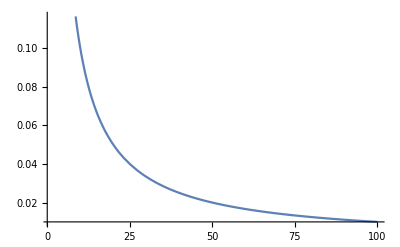

```mathematica
Plot[G[M],{M,1,100}]
```

### We see that the limit (as M grows) is zero also if q = 1/2.